### Gell - Mann Matrix representation of SU (3)

```mathematica
λ1={{0,1,0},{1,0,0},{0,0,0}}
λ2={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}}
λ3={{1,0,0},{0,-1,0},{0,0,0}}
λ4={{0,0,1},{0,0,0},{1,0,0}}
λ5={{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}}
λ6={{0,0,0},{0,0,1},{0,1,0}}
λ7={{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}}
λ8={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3]
```

{{0,1,0},{1,0,0},{0,0,0}}

{{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}}

{{1,0,0},{0,-1,0},{0,0,0}}

{{0,0,1},{0,0,0},{1,0,0}}

{{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}}

{{0,0,0},{0,0,1},{0,1,0}}

{{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}}

{{1/(√3),0,0},{0,1/(√3),0},{0,0,-2/(√3)}}

### F - spin representation of SU (3)

```mathematica
F1= λ1/2
F2= λ2/2
F3= λ3/2
F4= λ4/2
F5= λ5/2
F6= λ6/2
F7= λ7/2
F8= λ8/2
```

{{0,1/2,0},{1/2,0,0},{0,0,0}}

{{0,-ⅈ/2,0},{ⅈ/2,0,0},{0,0,0}}

{{1/2,0,0},{0,-1/2,0},{0,0,0}}

{{0,0,1/2},{0,0,0},{1/2,0,0}}

{{0,0,-ⅈ/2},{0,0,0},{ⅈ/2,0,0}}

{{0,0,0},{0,0,1/2},{0,1/2,0}}

{{0,0,0},{0,0,-ⅈ/2},{0,ⅈ/2,0}}

{{1/(2 √3),0,0},{0,1/(2 √3),0},{0,0,-1/(√3)}}

```mathematica
Y=2F8 / Sqrt[3]

Iplus=F1+ ⅈ F2
Iminus=F1- ⅈ F2
I0=F3

Vplus=F4+ ⅈ F5
Vminus=F4- ⅈ F5
V0= (Vplus.Vminus-Vminus.Vplus)/2

Uplus=F6+ ⅈ F7
Uminus=F6- ⅈ F7
U0= (Uplus.Uminus-Uminus.Uplus)/2
```

{{1/3,0,0},{0,1/3,0},{0,0,-2/3}}

{{0,1,0},{0,0,0},{0,0,0}}

{{0,0,0},{1,0,0},{0,0,0}}

{{1/2,0,0},{0,-1/2,0},{0,0,0}}

{{0,0,1},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{1,0,0}}

{{1/2,0,0},{0,0,0},{0,0,-1/2}}

{{0,0,0},{0,0,1},{0,0,0}}

{{0,0,0},{0,0,0},{0,1,0}}

{{0,0,0},{0,1/2,0},{0,0,-1/2}}

```mathematica
CharacteristicPolynomial[I0,x]
CharacteristicPolynomial[U0,x]
CharacteristicPolynomial[V0,x]
```

x/4-x^3

x/4-x^3

x/4-x^3

```mathematica
Comm[A_,B_]:= A.B - B.A
```

```mathematica
Comm[I0,Iplus]
Comm[I0,Iminus]
```

{{0,1,0},{0,0,0},{0,0,0}}

{{0,0,0},{-1,0,0},{0,0,0}}

```mathematica
eIp[ι_] := Evaluate[MatrixExp[ⅈ ι Iplus]]
eIm[ι_] := Evaluate[MatrixExp[ⅈ ι Iminus]]
eIo[ι_] := Evaluate[MatrixExp[ⅈ ι I0]]

eUp[ιp_] := Evaluate[MatrixExp[ⅈ ιp Uplus]]
eUm[ιp_] := Evaluate[MatrixExp[ⅈ ιp Uminus]]
eU0[ιp_] := Evaluate[MatrixExp[ⅈ ιp U0]]

eVp[ιp_] := Evaluate[MatrixExp[ⅈ ιp Vplus]]
eVm[ιp_] := Evaluate[MatrixExp[ⅈ ιp Vminus]]
eV0[ιp_] := Evaluate[MatrixExp[ⅈ ιp V0]]
```

```mathematica
Hd=D[ιp[z],z] Iplus + D[μp[z],z] eIp[ιp[z]].Uplus. eIp[-ιp[z]] + D[νp[z],z] eIp[ιp[z]].eUp[μp[z]].Vplus.eUp[-μp[z]]. eIp[-ιp[z]] ;
Hd//TraditionalForm
```

(0 | ιp'(z) | ⅈ ιp(z) μp'(z)+νp'(z)
0 | 0 | μp'(z)
0 | 0 | 0)

#### Here we define a function which can calulate the matrix governing the system of differential equations

```mathematica
GetHamiltonian[list_]:=(s=0;Do[w= D[Part[list,iterator2,1],z]*IdentityMatrix[3];Do[w=w.Evaluate[MatrixExp[ Part[list,iterator1,1]*Part[list,iterator1,2]]],{iterator1,iterator2-1}];
w= w.Part[list,iterator2,2];Do[w=w.Evaluate[MatrixExp[-Part[list,iterator2-iterator1,1]*Part[list,iterator2-iterator1,2]]],{iterator1,iterator2-1}];s=s+w,{iterator2,Length[list]}];Return[s]);
GetPropagator[list_]:=(
w=IdentityMatrix[3];
Do[w=w.MatrixExp[ Part[list,iterator,1]*Part[list,iterator,2]],{iterator,Length[list]}];
Return[w]
);
```

#### Let us specify to list which contain the Su(3) matrices as well as the z dependent functions The order of the elements is important; ie. reflects the order of the matrices in the propergator (The two different lists refer to the two orders given in the manusrcipt)

```mathematica
list =List[{ⅈ ιp[z],Iplus},{ ⅈ Log[ ι0[z]],IdentityMatrix[3]},{ⅈ ιm[z],Iminus},
{ⅈ  νp[z],Vplus},{  ⅈ  Log[ ν0[z]],V0},{ⅈ  νm[z],Vminus},
{ⅈ μp[z],Uplus},{ⅈ  Log[  μ0[z]],U0},{ⅈ μm[z],Uminus}];
list2 =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ  Log[ι0[z]],I0},{ⅈ  Log[μ0[z]],U0},{ⅈ  Log[ν0[z]],V0},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],μ0[z], ν0[z],
νm[z], μm[z], ιm[z]};
listOfDerivatives={ ιp'[z], μp'[z],  νp'[z],
ι0'[z],μ0'[z], ν0'[z],
νm'[z], μm'[z], ιm'[z]};
```

#### No we can easily calculate the matrices caontaining the differential terms

```mathematica
(res=FullSimplify[GetHamiltonian[list]]);
H=({{0, g1, g2}, {g1, 0, g3}, {g2, g3, 0}});
eqs1=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs1,listOfDerivatives]];
eqs2=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
```

```mathematica
ode = Join[eqs2,{ιp[0]==0,ι0[0]==1,ιm[0]==0,νp[0]==0,ν0[0]==1,νm[0]==0,μp[0]==0,μ0[0]==1,μm[0]==0}];
```

```mathematica
sol = NDSolve[ode/.{g1->1,g2->1,g3->1},listOfFunctions,{z,0,15}]
```

{{ιp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ι0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μ0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ν0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ιm[z]→InterpolatingFunction[{{0., 15.}}, <>][z]}}

```mathematica
ss=FullSimplify[D[GetPropagator[list],z].Inverse[GetPropagator[list]]]//TraditionalForm
```

(((μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) ((2 ⅈ ι0(z) ιp(z) νm(z) μp'(z) (ν0(z))^(1+ⅈ/2)+2 ι0(z) (ιm(z) ιp(z)-1) νp(z) νm'(z) ν0(z)+ⅈ (2 ν0(z) (ι0'(z)+ⅈ ι0(z) ιp(z) ιm'(z))+ι0(z) (1-ιm(z) ιp(z)) ν0'(z)) (ν0(z))^ⅈ) (μ0(z))^(1+ⅈ)-2 ι0(z) ν0(z) (ιm(z) (ν0(z))^(ⅈ/2)-ⅈ μp(z) νm(z)) (ιp(z) (ν0(z))^(ⅈ/2) μp(z)+ⅈ (ιm(z) ιp(z)-1) νp(z)) μm'(z) μ0(z)+ι0(z) ν0(z) (νm(z) (2 ιp(z) μp(z) (ν0(z))^(ⅈ/2)-ⅈ νp(z))+ⅈ ιm(z) ιp(z) (νm(z) νp(z)+(ν0(z))^ⅈ)) μ0'(z) (μ0(z))^ⅈ))/(2 ι0(z)) | 1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) (2 μ0(z) ν0(z) (ⅈ (ν0(z))^(ⅈ/2) (ιm(z) ιp(z)-1)+ιp(z) μp(z) νm(z)) (ιp(z) (ν0(z))^(ⅈ/2) μp(z)+ⅈ (ιm(z) ιp(z)-1) νp(z)) μm'(z)+(μ0(z))^ⅈ (2 (ν0(z))^(1+ⅈ/2) νm(z) (μ0(z) μp'(z)-ⅈ μp(z) μ0'(z)) (ιp(z))^2+(ιm(z) ιp(z)-1) ν0(z) νp(z) (νm(z) μ0'(z)-2 ⅈ μ0(z) νm'(z)) ιp(z)+(ν0(z))^ⅈ (ν0(z) (2 ⅈ μ0(z) (ιm'(z) (ιp(z))^2+ιp'(z))+ιp(z) (ιm(z) ιp(z)-1) μ0'(z))+ιp(z) (1-ιm(z) ιp(z)) μ0(z) ν0'(z)))) | 1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) ((ιm(z) ιp(z)-1) ν0(z) (2 ⅈ μ0(z) μp(z) νm(z) μm'(z)+(μ0(z))^ⅈ (νm(z) μ0'(z)-2 ⅈ μ0(z) νm'(z))) (νp(z))^2+2 ιp(z) (ν0(z))^(1+ⅈ/2) νm(z) (μ0(z) μm'(z) (μp(z))^2+(μ0(z))^ⅈ (μ0(z) μp'(z)-ⅈ μp(z) μ0'(z))) νp(z)-2 ιp(z) (ν0(z))^(1+(3 ⅈ)/2) (μ0(z) μm'(z) (μp(z))^2+(μ0(z))^ⅈ (μ0(z) μp'(z)-ⅈ μp(z) μ0'(z)))-(ιm(z) ιp(z)-1) (ν0(z))^ⅈ (2 ⅈ μ0(z) μp(z) ν0(z) νp(z) μm'(z)+(μ0(z))^ⅈ (2 μ0(z) νp(z) ν0'(z)+ν0(z) (νp(z) μ0'(z)+2 ⅈ μ0(z) νp'(z)))))
1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) (2 μ0(z) ν0(z) (ⅈ (ν0(z))^(ⅈ/2) ιm(z)+μp(z) νm(z)) ((ν0(z))^(ⅈ/2) μp(z)+ⅈ ιm(z) νp(z)) μm'(z)+(μ0(z))^ⅈ (2 νm(z) (μ0(z) μp'(z)-ⅈ μp(z) μ0'(z)) (ν0(z))^(1+ⅈ/2)+ιm(z) νp(z) (νm(z) μ0'(z)-2 ⅈ μ0(z) νm'(z)) ν0(z)+(ιm(z) ν0(z) μ0'(z)+μ0(z) (2 ⅈ ν0(z) ιm'(z)-ιm(z) ν0'(z))) (ν0(z))^ⅈ)) | ((μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) (2 ι0(z) μ0(z) ν0(z) ((ιm(z) ιp(z)-1) (ν0(z))^(ⅈ/2)-ⅈ ιp(z) μp(z) νm(z)) ((ν0(z))^(ⅈ/2) μp(z)+ⅈ ιm(z) νp(z)) μm'(z)+(μ0(z))^ⅈ (-2 ι0(z) ιp(z) νm(z) (μp(z) μ0'(z)+ⅈ μ0(z) μp'(z)) (ν0(z))^(1+ⅈ/2)+ι0(z) ιm(z) ιp(z) νp(z) (-ⅈ νm(z) μ0'(z)-2 μ0(z) νm'(z)) ν0(z)+ⅈ (ι0(z) (1-ιm(z) ιp(z)) ν0(z) μ0'(z)+μ0(z) (2 ν0(z) (ι0'(z)-ⅈ ι0(z) ιp(z) ιm'(z))+ι0(z) ιm(z) ιp(z) ν0'(z))) (ν0(z))^ⅈ)))/(2 ι0(z)) | 1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) (2 ⅈ (ⅈ ιm(z) ν0(z) νm'(z) (νp(z))^2-(ν0(z))^(1+ⅈ/2) νm(z) μp'(z) νp(z)+(ν0(z))^(1+(3 ⅈ)/2) μp'(z)+ιm(z) (ν0(z))^ⅈ (νp(z) ν0'(z)+ⅈ ν0(z) νp'(z))) (μ0(z))^(1+ⅈ)+2 ⅈ μp(z) ν0(z) ((ν0(z))^(ⅈ/2) μp(z)+ⅈ ιm(z) νp(z)) ((ν0(z))^ⅈ-νm(z) νp(z)) μm'(z) μ0(z)+ν0(z) (2 (ν0(z))^(ⅈ/2) μp(z)+ⅈ ιm(z) νp(z)) ((ν0(z))^ⅈ-νm(z) νp(z)) μ0'(z) (μ0(z))^ⅈ)
1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^-ⅈ (2 ⅈ νm'(z) (μ0(z))^(1+ⅈ)+2 (ιm(z) (ν0(z))^(ⅈ/2)-ⅈ μp(z) νm(z)) μm'(z) μ0(z)-νm(z) μ0'(z) (μ0(z))^ⅈ) | 1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^-ⅈ (ιp(z) ((μ0(z))^ⅈ (ⅈ νm(z) μ0'(z)+2 μ0(z) νm'(z))-2 μ0(z) μp(z) νm(z) μm'(z))-2 ⅈ (ιm(z) ιp(z)-1) μ0(z) (ν0(z))^(ⅈ/2) μm'(z)) | (ⅈ ι0'(z))/(ι0(z))+1/2 (μ0(z))^(-1-ⅈ) (ν0(z))^(-1-ⅈ) (2 μ0(z) μp(z) ν0(z) ((ν0(z))^ⅈ-νm(z) νp(z)) μm'(z)+(μ0(z))^ⅈ (ν0(z) νp(z) (ⅈ νm(z) μ0'(z)+2 μ0(z) νm'(z))-ⅈ (ν0(z))^ⅈ (ν0(z) μ0'(z)+μ0(z) ν0'(z)))))

```mathematica
N[MatrixExp[ 1.0ⅈ ({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})]]//TraditionalForm
```

(0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
(GetPropagator[list ]/.sol/.{z->1.0})[[1]]//TraditionalForm
```

(0.221486-0.257881 ⅈ | -0.318816+0.583591 ⅈ | -0.318816+0.583589 ⅈ
-0.318817+0.583589 ⅈ | 0.221486-0.257881 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | -0.318817+0.583589 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
Chop[ss/.sol/.D[sol,z]/.{z->.000001}]
```

{{(5.95212×10^-6-9.98872×10^-10 ⅈ | 2.97606×10^-6+1. ⅈ | 2.97606×10^-6+1. ⅈ
-2.97606×10^-6+1. ⅈ | 0.+9.94395×10^-10 ⅈ | 2.97606×10^-6+1. ⅈ
-2.97606×10^-6+1. ⅈ | -2.97606×10^-6+1. ⅈ | -5.95212×10^-6)}}

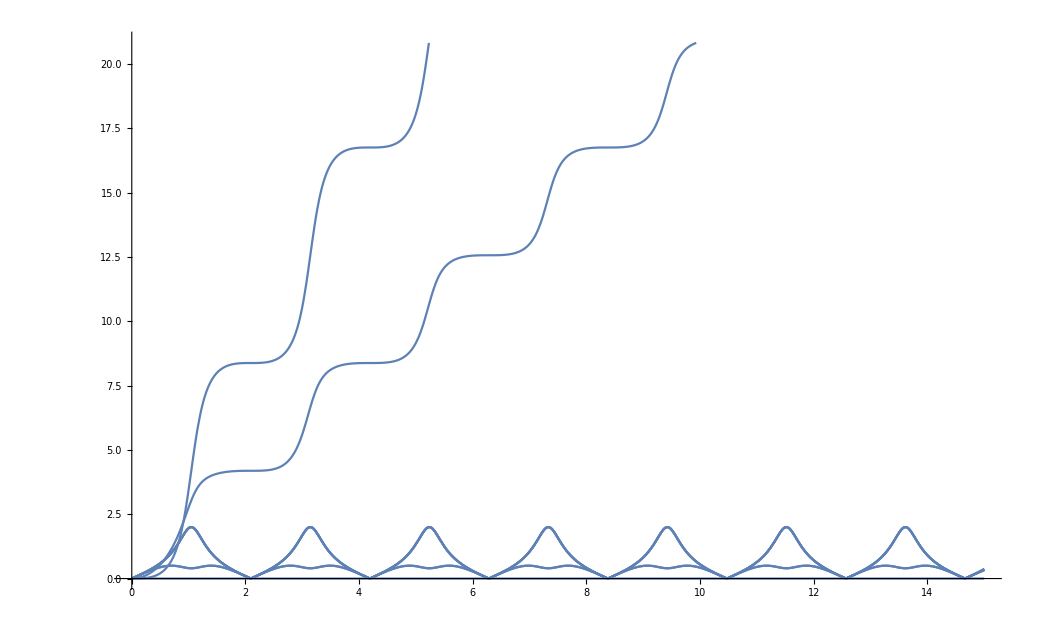

```mathematica
Plot[{ Abs[ιp[z]], Abs[Log[ι0[z]]], Abs[ιm[z]],Abs[νp[z]], Abs[Log[ν0[z]]],Abs[νm[z]],Abs[μp[z]],Abs[Log[μ0[z]]],Abs[μm[z]]}/.sol,{z,0,15}]
```

```mathematica
eqs2
```

{ιp'[z]==g1+g1 ιp[z]^2-ⅈ g3 νp[z]+g2 ιp[z] νp[z],μp'[z]==(g3+ⅈ g2 ιp[z]) μp[z]^2 ν0[z]^(ⅈ/2)-2 μp[z] (g1 ιp[z]+ιm[z] (-ⅈ g3+g2 ιp[z]) νp[z])+((g3+ιm[z] (-ⅈ g2-g3 ιp[z])) ν0[z]^(ⅈ/2))/(ν0[z]^ⅈ-νm[z] νp[z]),νp'[z]==g2-ⅈ g3 ιp[z]+g1 ιp[z] νp[z]+g2 νp[z]^2,ι0'[z]==0,μ0'[z]==2 μ0[z] (ⅈ g1 ιp[z]+(-ⅈ g3+g2 ιp[z]) μp[z] ν0[z]^(ⅈ/2)+g3 ιm[z] νp[z]+ⅈ g2 ιm[z] ιp[z] νp[z]),ν0'[z]==-2 ⅈ ν0[z] (g1 ιp[z]+g2 νp[z]),νm'[z]==(g2+ⅈ ιm[z] (g3+ⅈ g2 ιp[z])) ν0[z]^ⅈ+νm[z] (g1 ιp[z]+ιm[z] (-ⅈ g3+g2 ιp[z]) νp[z]),μm'[z]==(g3+ⅈ g2 ιp[z]) μ0[z]^ⅈ ν0[z]^(ⅈ/2),ιm'[z]==g1+ιm[z] (-2 g1 ιp[z]+ⅈ ιm[z] (g3+ⅈ g2 ιp[z]) νp[z])+((ⅈ g3+ιm[z] (g2-ⅈ g3 ιp[z])) νm[z])/(ν0[z]^ⅈ-νm[z] νp[z])}

#### Let us specify to list which contain the Su(3) matrices as well as the z dependent functions The order of the elements is important; ie. reflects the order of the matrices in the propergator (The two different lists refer to the two orders given in the manusrcipt)

```mathematica
list =List[{ⅈ ιp[z],Iplus},{ ⅈ  ι0[z],I0},{ⅈ ιm[z],Iminus},
{ⅈ  νp[z],Vplus},{  ⅈ   ν0[z],V0},{ⅈ  νm[z],Vminus},
{ⅈ μp[z],Uplus},{ⅈ    μ0[z],U0},{ⅈ μm[z],Uminus}];
list2 =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ ι0[z],I0},{ⅈ μ0[z],U0},{ⅈ  ν0[z],V0},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
list3 =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ ι0[z],I0},{ⅈ μ0[z],Y},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];

listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],μ0[z], ν0[z],
νm[z], μm[z], ιm[z]};
listOfDerivatives={ ιp'[z], μp'[z],  νp'[z],
ι0'[z],μ0'[z], ν0'[z],
νm'[z], μm'[z], ιm'[z]};
```

#### No we can easily calculate the matrices caontaining the differential terms

```mathematica
(res=FullSimplify[GetHamiltonian[list3]]);
H=({{0, g1, g2}, {g1, 0, g3}, {g2, g3, 0}});
eqs1=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs1,listOfDerivatives]];
eqs2=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
```

{{1/6 ⅇ^(-ⅈ (ι0[z]+μ0[z])) (-6 ⅇ^(ⅈ μ0[z]) ιp[z] ιm'[z]+ⅈ ⅇ^(ⅈ (ι0[z]+μ0[z])) (3 ι0'[z]+2 μ0'[z])+6 ⅇ^(1/2 ⅈ ι0[z]) (ιp[z] μp[z]-ⅈ νp[z]) (μm[z] ιm'[z]-ⅈ νm'[z])),ⅇ^(-ⅈ (ι0[z]+μ0[z])) (ⅇ^(ⅈ μ0[z]) (ⅈ ιp[z]^2 ιm'[z]+ⅇ^(ⅈ ι0[z]) (ιp[z] ι0'[z]+ⅈ ιp'[z]))-ⅈ ⅇ^(1/2 ⅈ ι0[z]) (ιp[z] μp[z]-ⅈ νp[z]) (ⅇ^(ⅈ ι0[z]) μm'[z]+ιp[z] (μm[z] ιm'[z]-ⅈ νm'[z]))),1/2 ⅇ^(-ⅈ (ι0[z]+μ0[z])) (-2 ⅇ^(1/2 ⅈ ι0[z]) (ιp[z] μp[z]-ⅈ νp[z]) (ⅇ^(ⅈ ι0[z]) μp[z] μm'[z]+νp[z] (ⅈ μm[z] ιm'[z]+νm'[z]))+ⅇ^(ⅈ μ0[z]) (2 ⅈ ιp[z] νp[z] ιm'[z]+ⅇ^(ⅈ ι0[z]) (νp[z] (ι0'[z]+2 μ0'[z])+ιp[z] (-ⅈ μp[z] (ι0'[z]-2 μ0'[z])-2 μp'[z])+2 ⅈ νp'[z])))},{ⅈ ⅇ^(-ⅈ ι0[z]) (ιm'[z]-ⅇ^(1/2 ⅈ (ι0[z]-2 μ0[z])) μp[z] (μm[z] ιm'[z]-ⅈ νm'[z])),1/6 ⅇ^(-ⅈ (ι0[z]+μ0[z])) (ⅇ^(ⅈ μ0[z]) (6 ιp[z] ιm'[z]-ⅈ ⅇ^(ⅈ ι0[z]) (3 ι0'[z]-2 μ0'[z]))-6 ⅇ^(1/2 ⅈ ι0[z]) μp[z] (ⅇ^(ⅈ ι0[z]) μm'[z]+ιp[z] (μm[z] ιm'[z]-ⅈ νm'[z]))),ⅇ^(-ⅈ ι0[z]) νp[z] ιm'[z]+ⅈ μp'[z]+1/2 μp[z] (-ι0'[z]+2 μ0'[z]+2 ⅈ ⅇ^(-1/2 ⅈ (ι0[z]+2 μ0[z])) (ⅇ^(ⅈ ι0[z]) μp[z] μm'[z]+νp[z] (ⅈ μm[z] ιm'[z]+νm'[z])))},{ⅇ^(-1/2 ⅈ (ι0[z]+2 μ0[z])) (-μm[z] ιm'[z]+ⅈ νm'[z]),ⅇ^(-1/2 ⅈ (ι0[z]+2 μ0[z])) (ⅈ ⅇ^(ⅈ ι0[z]) μm'[z]+ιp[z] (ⅈ μm[z] ιm'[z]+νm'[z])),-2/3 ⅈ μ0'[z]+ⅇ^(-1/2 ⅈ (ι0[z]+2 μ0[z])) (ⅇ^(ⅈ ι0[z]) μp[z] μm'[z]+νp[z] (ⅈ μm[z] ιm'[z]+νm'[z]))}}

```mathematica
ode = Remove[Join[eqs2,{ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,ν0[0]==0,νm[0]==0,μp[0]==0,μ0[0]==0,μm[0]==0}];
```

```mathematica
odef=FullSimplify[ode/.{g1->1,g2->1,g3->1}]
```

{(-ⅈ+ιp[z]) (ⅈ+ιp[z]+νp[z])==ιp'[z],μp'[z]==(ⅈ+μp[z]) (-ⅈ+μp[z]+ⅈ ιp[z] μp[z]+νp[z]),1+νp[z]^2+ιp[z] (-ⅈ+νp[z])==νp'[z],-ⅈ μp[z]+ιp[z] (2 ⅈ+μp[z])+ⅈ νp[z]+ι0'[z]==0,μ0'[z]==-3/2 ⅈ (μp[z]+ⅈ ιp[z] μp[z]+νp[z]),True,ⅇ^(1/2 ⅈ (ι0[z]+2 μ0[z]))==ⅇ^(ⅈ ι0[z]) μm[z] (ⅈ+μp[z])+νm'[z],μm'[z]==ⅇ^(-1/2 ⅈ (ι0[z]-2 μ0[z])) (1+ⅈ ιp[z]),ιm'[z]==ⅇ^(ⅈ ι0[z]) (1-ⅈ μp[z]),ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,ν0[0]==0,νm[0]==0,μp[0]==0,μ0[0]==0,μm[0]==0}

```mathematica
sol = NDSolve[odef,listOfFunctions,{z,0,15}]
```

NDSolve[{(-ⅈ+ιp[z]) (ⅈ+ιp[z]+νp[z])==ιp'[z],μp'[z]==(ⅈ+μp[z]) (-ⅈ+μp[z]+ⅈ ιp[z] μp[z]+νp[z]),1+νp[z]^2+ιp[z] (-ⅈ+νp[z])==νp'[z],-ⅈ μp[z]+ιp[z] (2 ⅈ+μp[z])+ⅈ νp[z]+ι0'[z]==0,μ0'[z]==-3/2 ⅈ (μp[z]+ⅈ ιp[z] μp[z]+νp[z]),True,ⅇ^(1/2 ⅈ (ι0[z]+2 μ0[z]))==ⅇ^(ⅈ ι0[z]) μm[z] (ⅈ+μp[z])+νm'[z],μm'[z]==ⅇ^(-1/2 ⅈ (ι0[z]-2 μ0[z])) (1+ⅈ ιp[z]),ιm'[z]==ⅇ^(ⅈ ι0[z]) (1-ⅈ μp[z]),ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,ν0[0]==0,νm[0]==0,μp[0]==0,μ0[0]==0,μm[0]==0},{ιp[z],μp[z],νp[z],ι0[z],μ0[z],ν0[z],νm[z],μm[z],ιm[z]},{z,0,15}]

```mathematica
ss=FullSimplify[D[GetPropagator[list],z].Inverse[GetPropagator[list]]]//TraditionalForm
```

(1/2 ⅇ^(-ⅈ (ι0(z)+μ0(z)+ν0(z))) (2 ⅇ^(1/2 ⅈ ν0(z)) (ⅈ (ⅇ^(ⅈ ι0(z)) ιm(z) νp(z)+ιp(z) ((μp(z))^2 νm(z)-(ιm(z))^2 νp(z))) μm'(z)+ⅇ^(ⅈ μ0(z)) ιp(z) νm(z) (μp(z) μ0'(z)+ⅈ μp'(z)))+ⅇ^(ⅈ ν0(z)) (ⅈ ⅇ^(ⅈ μ0(z)) (ιp(z) (2 ⅈ ιm'(z)+ιm(z) (μ0'(z)-ν0'(z)))+ⅇ^(ⅈ ι0(z)) (ι0'(z)+ν0'(z)))-2 ιm(z) ιp(z) μp(z) μm'(z))+(ⅇ^(ⅈ ι0(z))-ιm(z) ιp(z)) νp(z) (2 μp(z) νm(z) μm'(z)-ⅈ ⅇ^(ⅈ μ0(z)) (νm(z) μ0'(z)-2 ⅈ νm'(z)))) | 1/2 ⅇ^(-ⅈ (ι0(z)+μ0(z)+ν0(z))) (2 ⅇ^(1/2 ⅈ ν0(z)) (ⅇ^(ⅈ μ0(z)) νm(z) (μp'(z)-ⅈ μp(z) μ0'(z)) (ιp(z))^2+(((μp(z))^2 νm(z)-(ιm(z))^2 νp(z)) (ιp(z))^2+2 ⅇ^(ⅈ ι0(z)) ιm(z) νp(z) ιp(z)-ⅇ^(2 ⅈ ι0(z)) νp(z)) μm'(z))+ⅇ^(ⅈ ν0(z)) (2 ⅈ ιp(z) (ιm(z) ιp(z)-ⅇ^(ⅈ ι0(z))) μp(z) μm'(z)+ⅇ^(ⅈ μ0(z)) ((2 ⅈ ιm'(z)+ιm(z) (μ0'(z)-ν0'(z))) (ιp(z))^2+ⅇ^(ⅈ ι0(z)) (2 ⅈ ιp'(z)+ιp(z) (2 ι0'(z)-μ0'(z)+ν0'(z)))))+ιp(z) (ιm(z) ιp(z)-ⅇ^(ⅈ ι0(z))) νp(z) (2 ⅈ μp(z) νm(z) μm'(z)+ⅇ^(ⅈ μ0(z)) (νm(z) μ0'(z)-2 ⅈ νm'(z)))) | 1/2 ⅇ^(-1/2 ⅈ (ι0(z)+2 (μ0(z)+ν0(z)))) (-(ⅇ^(ⅈ ι0(z))-ιm(z) ιp(z)) (2 ⅈ μp(z) νm(z) μm'(z)+ⅇ^(ⅈ μ0(z)) (νm(z) μ0'(z)-2 ⅈ νm'(z))) (νp(z))^2+2 ⅇ^(1/2 ⅈ ν0(z)) ιp(z) νm(z) (μm'(z) (μp(z))^2+ⅇ^(ⅈ μ0(z)) (μp'(z)-ⅈ μp(z) μ0'(z))) νp(z)-2 ⅇ^(3/2 ⅈ ν0(z)) ιp(z) (μm'(z) (μp(z))^2+ⅇ^(ⅈ μ0(z)) (μp'(z)-ⅈ μp(z) μ0'(z)))+ⅇ^(ⅈ ν0(z)) (ⅇ^(ⅈ ι0(z))-ιm(z) ιp(z)) (2 ⅈ μp(z) νp(z) μm'(z)+ⅇ^(ⅈ μ0(z)) (νp(z) (μ0'(z)+2 ν0'(z))+2 ⅈ νp'(z))))
1/2 ⅇ^(-ⅈ (ι0(z)+μ0(z)+ν0(z))) (2 (ⅈ ⅇ^(1/2 ⅈ ν0(z)) ιm(z)+μp(z) νm(z)) (ⅇ^(1/2 ⅈ ν0(z)) μp(z)+ⅈ ιm(z) νp(z)) μm'(z)+ⅇ^(ⅈ μ0(z)) (2 ⅇ^(1/2 ⅈ ν0(z)) νm(z) (μp'(z)-ⅈ μp(z) μ0'(z))+ⅇ^(ⅈ ν0(z)) (2 ⅈ ιm'(z)+ιm(z) (μ0'(z)-ν0'(z)))+ιm(z) νp(z) (νm(z) μ0'(z)-2 ⅈ νm'(z)))) | 1/2 ⅇ^(-ⅈ (ι0(z)+μ0(z)+ν0(z))) ((sin(ι0(z)+μ0(z)+ν0(z))-ⅈ cos(ι0(z)+μ0(z)+ν0(z))) ι0'(z)-2 (ⅇ^(1/2 ⅈ ν0(z)) (ⅇ^(ⅈ ι0(z))-ιm(z) ιp(z))+ⅈ ιp(z) μp(z) νm(z)) (ⅇ^(1/2 ⅈ ν0(z)) μp(z)+ⅈ ιm(z) νp(z)) μm'(z)+ⅇ^(ⅈ μ0(z)) (ⅈ ⅇ^(ⅈ (ι0(z)+ν0(z))) μ0'(z)+ιp(z) (-2 ⅇ^(1/2 ⅈ ν0(z)) νm(z) (μp(z) μ0'(z)+ⅈ μp'(z))+ⅇ^(ⅈ ν0(z)) (2 ιm'(z)-ⅈ ιm(z) (μ0'(z)-ν0'(z)))+ιm(z) νp(z) (-ⅈ νm(z) μ0'(z)-2 νm'(z))))) | 1/2 ⅇ^(-1/2 ⅈ (ι0(z)+2 (μ0(z)+ν0(z)))) (2 ⅈ μp(z) (ⅇ^(1/2 ⅈ ν0(z)) μp(z)+ⅈ ιm(z) νp(z)) (ⅇ^(ⅈ ν0(z))-νm(z) νp(z)) μm'(z)+ⅇ^(ⅈ μ0(z)) (ιm(z) (-ⅈ νm(z) μ0'(z)-2 νm'(z)) (νp(z))^2-2 ⅇ^(1/2 ⅈ ν0(z)) νm(z) (μp(z) μ0'(z)+ⅈ μp'(z)) νp(z)+2 ⅇ^(3/2 ⅈ ν0(z)) (μp(z) μ0'(z)+ⅈ μp'(z))+ⅈ ⅇ^(ⅈ ν0(z)) ιm(z) (νp(z) (μ0'(z)+2 ν0'(z))+2 ⅈ νp'(z))))
1/2 ⅇ^(-1/2 ⅈ (ι0(z)+2 (μ0(z)+ν0(z)))) (2 (ⅇ^(1/2 ⅈ ν0(z)) ιm(z)-ⅈ μp(z) νm(z)) μm'(z)+ⅇ^(ⅈ μ0(z)) (2 ⅈ νm'(z)-νm(z) μ0'(z))) | 1/2 ⅇ^(-1/2 ⅈ (ι0(z)+2 (μ0(z)+ν0(z)))) (2 ⅈ ⅇ^(1/2 ⅈ ν0(z)) (ⅇ^(ⅈ ι0(z))-ιm(z) ιp(z)) μm'(z)+ιp(z) (ⅇ^(ⅈ μ0(z)) (ⅈ νm(z) μ0'(z)+2 νm'(z))-2 μp(z) νm(z) μm'(z))) | -1/2 ⅈ (1-ⅇ^(-ⅈ ν0(z)) νm(z) νp(z)) μ0'(z)+ⅇ^(-ⅈ (μ0(z)+ν0(z))) μp(z) (ⅇ^(ⅈ ν0(z))-νm(z) νp(z)) μm'(z)-1/2 ⅈ ν0'(z)+ⅇ^(-ⅈ ν0(z)) νp(z) νm'(z))

```mathematica
N[MatrixExp[ 1.0ⅈ ({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})]]//TraditionalForm
```

(0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ | -0.318816+0.583589 ⅈ
-0.318816+0.583589 ⅈ | -0.318816+0.583589 ⅈ | 0.221486-0.257882 ⅈ)

```mathematica
(GetPropagator[list ]/.sol/.{z->1.0})[[1]]//TraditionalForm
```

(ⅇ^(1/2 ⅈ ν0(1.)) (ⅇ^(1/2 ⅈ ι0(1.))-ⅇ^(-1/2 ⅈ ι0(1.)) ιm(1.) ιp(1.))-ⅇ^(-1/2 ⅈ ν0(1.)) (ⅇ^(1/2 ⅈ ι0(1.))-ⅇ^(-1/2 ⅈ ι0(1.)) ιm(1.) ιp(1.)) νm(1.) νp(1.) | ⅈ ⅇ^(1/2 ⅈ μ0(1.)-1/2 ⅈ ι0(1.)) ιp(1.)+ⅈ ⅇ^(-1/2 ⅈ μ0(1.)) μm(1.) (ⅈ ⅇ^(-1/2 ⅈ ν0(1.)) (ⅇ^(1/2 ⅈ ι0(1.))-ⅇ^(-1/2 ⅈ ι0(1.)) ιm(1.) ιp(1.)) νp(1.)-ⅇ^(-1/2 ⅈ ι0(1.)) ιp(1.) μp(1.)) | ⅇ^(-1/2 ⅈ μ0(1.)) (ⅈ ⅇ^(-1/2 ⅈ ν0(1.)) (ⅇ^(1/2 ⅈ ι0(1.))-ⅇ^(-1/2 ⅈ ι0(1.)) ιm(1.) ιp(1.)) νp(1.)-ⅇ^(-1/2 ⅈ ι0(1.)) ιp(1.) μp(1.))
ⅈ ⅇ^(1/2 ⅈ ν0(1.)-1/2 ⅈ ι0(1.)) ιm(1.)-ⅈ ⅇ^(-1/2 ⅈ ι0(1.)-1/2 ⅈ ν0(1.)) ιm(1.) νm(1.) νp(1.) | ⅈ ⅇ^(-1/2 ⅈ μ0(1.)) μm(1.) (ⅈ ⅇ^(-1/2 ⅈ ι0(1.)) μp(1.)-ⅇ^(-1/2 ⅈ ι0(1.)-1/2 ⅈ ν0(1.)) ιm(1.) νp(1.))+ⅇ^(1/2 ⅈ μ0(1.)-1/2 ⅈ ι0(1.)) | ⅇ^(-1/2 ⅈ μ0(1.)) (ⅈ ⅇ^(-1/2 ⅈ ι0(1.)) μp(1.)-ⅇ^(-1/2 ⅈ ι0(1.)-1/2 ⅈ ν0(1.)) ιm(1.) νp(1.))
ⅈ ⅇ^(-1/2 ⅈ ν0(1.)) νm(1.) | ⅈ ⅇ^(-1/2 ⅈ μ0(1.)-1/2 ⅈ ν0(1.)) μm(1.) | ⅇ^(-1/2 ⅈ μ0(1.)-1/2 ⅈ ν0(1.)))

```mathematica
Chop[ss/.sol/.D[sol,z]/.{z->.000001}]
```

(1)/.NDSolve[{ιp'[1.×10^-6]==1+ιp[1.×10^-6]^2+ⅇ^(1/2 ⅈ ι0[1.×10^-6]) (-ⅈ+ιp[1.×10^-6]) νp[1.×10^-6],μp'[1.×10^-6]==(ⅇ^(-1/2 ⅈ (ι0[1.×10^-6]-ν0[1.×10^-6])) (ⅇ^(ⅈ ι0[1.×10^-6])+ιm[1.×10^-6] (-ⅈ-ιp[1.×10^-6])-(1+ⅈ ιp[1.×10^-6]) μp[1.×10^-6]^2 (ⅇ^(ⅈ ν0[1.×10^-6])-νm[1.×10^-6] νp[1.×10^-6])))/(ⅇ^(ⅈ ν0[1.×10^-6])-νm[1.×10^-6] νp[1.×10^-6])+ⅈ μp[1.×10^-6] μ0'[1.×10^-6],νp'[1.×10^-6]==ⅇ^(-1/2 ⅈ ι0[1.×10^-6]) (1+ⅇ^(1/2 ⅈ ν0[1.×10^-6]) μp[1.×10^-6] νp[1.×10^-6]+(ⅇ^(ⅈ ι0[1.×10^-6])+ⅈ ιm[1.×10^-6]) νp[1.×10^-6]^2+ⅈ ιp[1.×10^-6] (-1+νp[1.×10^-6] (ⅇ^(1/2 ⅈ ν0[1.×10^-6]) μp[1.×10^-6]+ⅈ ιm[1.×10^-6] νp[1.×10^-6])))-1/2 ⅈ νp[1.×10^-6] μ0'[1.×10^-6],12,μp[0]==0,μ0[0]==0,μm[0]==0},{ιp[1.×10^-6],μp[1.×10^-6],νp[1.×10^-6],ι0[1.×10^-6],μ0[1.×10^-6],ν0[1.×10^-6],νm[1.×10^-6],μm[1.×10^-6],ιm[1.×10^-6]},{1.×10^-6,0,15}]/.1
 |  |  |  |

```mathematica
Plot[{ Abs[ιp[z]], Abs[Log[ι0[z]]], Abs[ιm[z]],Abs[νp[z]], Abs[Log[ν0[z]]],Abs[νm[z]],Abs[μp[z]],Abs[Log[μ0[z]]],Abs[μm[z]]}/.sol,{z,0,15}]
```

-Graphics-

```mathematica
eqs2
```

{ιp'[z]==g1 (1+ιp[z]^2)+ⅇ^(1/2 ⅈ ι0[z]) (-ⅈ g3+g2 ιp[z]) νp[z],μp'[z]==(ⅇ^(-1/2 ⅈ (ι0[z]-ν0[z])) (ⅇ^(ⅈ ι0[z]) g3+ιm[z] (-ⅈ g2-g3 ιp[z])-(g3+ⅈ g2 ιp[z]) μp[z]^2 (ⅇ^(ⅈ ν0[z])-νm[z] νp[z])))/(ⅇ^(ⅈ ν0[z])-νm[z] νp[z])+ⅈ μp[z] μ0'[z],νp'[z]==ⅇ^(-1/2 ⅈ ι0[z]) (g2+ⅇ^(1/2 ⅈ ν0[z]) g3 μp[z] νp[z]+(ⅇ^(ⅈ ι0[z]) g2+ⅈ g3 ιm[z]) νp[z]^2+ⅈ ιp[z] (-g3+g2 νp[z] (ⅇ^(1/2 ⅈ ν0[z]) μp[z]+ⅈ ιm[z] νp[z])))-1/2 ⅈ νp[z] μ0'[z],ι0'[z]==2 ⅈ ⅇ^(-1/2 ⅈ ι0[z]) (-ⅇ^(1/2 ⅈ ι0[z]) g1 ιp[z]+ⅇ^(1/2 ⅈ ν0[z]) (g3+ⅈ g2 ιp[z]) μp[z]+ⅈ g3 ιm[z] νp[z]-g2 ιm[z] ιp[z] νp[z])+μ0'[z],True,ν0'[z]==ⅇ^(-1/2 ⅈ ι0[z]) (-2 ⅈ ⅇ^(ⅈ ι0[z]) g2 νp[z]+2 (g3+ⅈ g2 ιp[z]) (-ⅈ ⅇ^(1/2 ⅈ ν0[z]) μp[z]+ιm[z] νp[z])-ⅇ^(1/2 ⅈ ι0[z]) μ0'[z]),νm'[z]==ⅇ^(-1/2 ⅈ (ι0[z]-2 ν0[z])) (ⅇ^(ⅈ ι0[z]) g2+ⅈ ιm[z] (g3+ⅈ g2 ιp[z]))+ⅇ^(-1/2 ⅈ (ι0[z]-ν0[z])) (g3+ⅈ g2 ιp[z]) μp[z] νm[z]-1/2 ⅈ νm[z] μ0'[z],μm'[z]==ⅇ^(-1/2 ⅈ (ι0[z]-2 μ0[z]-ν0[z])) (g3+ⅈ g2 ιp[z]),ιm'[z]==ⅇ^(-1/2 ⅈ ι0[z]) (ⅇ^(3/2 ⅈ ι0[z]) g1-2 ⅇ^(1/2 ⅈ ν0[z]) ιm[z] (g3+ⅈ g2 ιp[z]) μp[z]-ⅈ g3 ιm[z]^2 νp[z]+g2 ιm[z]^2 ιp[z] νp[z]+((ⅈ ⅇ^(ⅈ ι0[z]) g3+ιm[z] (g2-ⅈ g3 ιp[z])) νm[z])/(ⅇ^(ⅈ ν0[z])-νm[z] νp[z])+ⅈ ⅇ^(1/2 ⅈ ι0[z]) ιm[z] μ0'[z])}